```mathematica
SetDirectory["/home/student/compphys/week8"]
```

/home/student/compphys/week8

```mathematica
data=Partition[ReadList["!./nbody 10 10 2 .001 100 100",Number],41];
```

```mathematica
data[[1]]
```

{0.1,0.0982261,0.000635561,0.175986,1.12526,0.174324,2.2938,0.0197242,3.51988,1.07564,0.144044,1.17804,1.22117,1.27132,2.32987,1.00386,3.37845,2.07807,0.0343587,2.16573,1.16877,-0.632566,-0.0127604,1.52023,0.0297586,1.76713,0.539434,-1.0611,1.53286,0.778127,1.66997,-1.03828,1.1236,1.56192,0.682039,0.0312423,0.0266667,-1.3394,0.38795,1.02498,0.378237}

```mathematica
show[l_,n_,L_]:=Graphics[{{FaceForm[],EdgeForm[Thick],Rectangle[{0,0},{L,L}]},{AbsolutePointSize[10],Table[Point[l[[2*i;;2*i+1]]],{i,n}]}}]
```

```mathematica
data//Length
```

200

```mathematica
ListAnimate[Table[show[data[[k]],10,10],{k,200}]]
```

```mathematica
ken[l_,n_]:=Sum[e^2,{e,l[[2n+2;;4n+1]]}]/2;
```

```mathematica
ken[data[[1]],10]
```

10.6905

```mathematica
pot[l_,n_]:=Module[{v},
v[r_]:=4((1/r)^12-(1/r)^6);
Sum[v[Norm[l[[2*i;;2*i+1]]-l[[2*j;;2*j+1]]]],{i,n},{j,i+1,n}]]
```

```mathematica
pot[data[[1]],10]
```

-10.6901

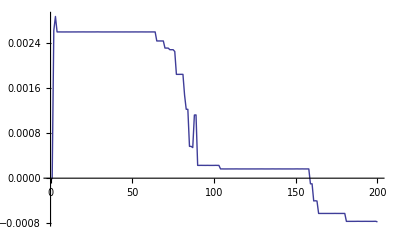

```mathematica
ListLinePlot[Table[ken[d,10]+pot[d,10],{d,data}]]
```

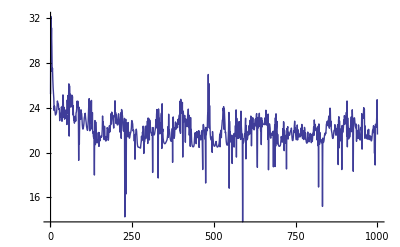

```mathematica
ListLinePlot[Table[ken[d,10],{d,data}],PlotRange->All]
```

```mathematica
Mean[Table[ken[d,10],{d,data[[200;;]]}]]
```

21.8206

```mathematica
StandardDeviation[Table[ken[d,10],{d,data[[200;;]]}]]/Sqrt[Length[Table[ken[d,10],{d,data[[200;;]]}]]]
```

0.0412136